# Sizzling Magnets [v5] - Theorie

## §1. Vector Potential A at z_0k

```mathematica
R=2.1*10^-2 (* R = length of major axis -- along x-direction *)
```

0.021

```mathematica
r=0.69*10^-2 (* r = length of minor axis -- along y- and z- directions *)
```

0.0069

```mathematica
Show[Graphics3D[Ellipsoid[{0,0,0},{R,r,r}]],Axes->True,AxesStyle->Black]
```

-Graphics3D-

```mathematica
b=R/r
```

3.04348

```mathematica
g[x1_,x2_,x3_,y1_,y2_,y3_]:=Norm[{x1,x2,x3}-{y1,y2,y3}]^3
```

```mathematica
z0=8*10^-2
```

2/25

```mathematica
f[x_,y_,z_]:=(z0-z)/g[0,0,z0,x,y,z]
```

```mathematica
NIntegrate[f[x,y,z],{x,y,z}∈Ellipsoid[{0,0,0},{R,r,r}]]
(* this is the integral Iz -- then A = mu0 M / 4pi x Iz k *)
```

0.00064269

```mathematica
(4π b)/z0∫_0^r x^2/(√(z0^2+(b^2-1)x^2))ⅆx (* value of the above volume integral -- should give Iz at z0 k *)
```

0.00064269

```mathematica
JZaxis[z_]:=(2π b)/(b^2-1)(r √((b^2-1)(r/z)^2+1)-z/(√(b^2-1))ArcSinh[(r √(b^2-1))/z]) 
(* closed form of above integral for b > 1 -- if b = 1 we end up with Luca's result for spherical magnets *)
```

```mathematica
JZaxis[z0]
```

0.00064269

## §2. Vector Potential A Over R^3

```mathematica
J[x0_,y0_,z0_]:=NIntegrate[({x0,y0,z0}-{x,y,z})/(Norm[{x0,y0,z0}-{x,y,z}])^3,
								{x,y,z}∈Ellipsoid[{0,0,0},{R,r,r}],AccuracyGoal->20] 
(* this is the integral I -- then A = mu0 M / 4pi x I *)
```

```mathematica
J[0,0,z0]
```

{0.,0.,0.00064269}

```mathematica
J[0,z0*Sin[π/3],z0*Cos[π/3]]
```

{0.,0.000556585,0.000321345}

```mathematica
JZaxis[z0]*Sin[π/3]
```

0.000556585

```mathematica
J[0,57,29]
```

{0.,9.12633×10^-10,4.64322×10^-10}

```mathematica
{0,JZaxis[√(57^2+29^2)]*57/(√(57^2+29^2)),JZaxis[√(57^2+29^2)]*29/(√(57^2+29^2))}
```

{0,9.12633×10^-10,4.64322×10^-10}

```mathematica
Norm[J[0,z0*Sin[π/3],z0*Cos[π/3]]]
```

0.00064269

```mathematica
M={0,0,1} (* magnetization; scalable units *)
```

{0,0,1}

```mathematica
J[12,8,5]
```

{1.41304×10^-8,9.42025×10^-9,5.88766×10^-9}

```mathematica
A[x_,y_,z_]:=10^-7*Cross[M,J[x,y,z]] (* vector potential A up to a factor of M *)
```

```mathematica
yy1 = 12*10^-2
```

3/25

```mathematica
zz1= 17 *10^-2(* (0, yy1, zz1) is the test location for verifying that A is theoretically correct *)
```

17/100

```mathematica
A[0,yy1,zz1]
```

{-5.56258×10^-12,0.,0.}

```mathematica
JZaxis[√(yy1^2+zz1^2)]*(-Norm[M])*(yy1/(√(yy1^2+zz1^2))) (* this is the theoretical value for A in the yz-plane *)
```

-0.0000556258

```mathematica
dds = 10^-3
```

1/1000

```mathematica
N[dds]
```

0.001

```mathematica
Ax[x_,y_,z_]:=A[x,y,z].{1,0,0}
```

```mathematica
Ay[x_,y_,z_]:=A[x,y,z].{0,1,0}
```

```mathematica
Az[x_,y_,z_]:=A[x,y,z].{0,0,1}
```

```mathematica
B[x_,y_,z_]:=
{(Az[x,y+dds,z]-Az[x,y,z])/dds-(Ay[x,y,z+dds]-Ay[x,y,z])/dds,
(Ax[x,y,z+dds]-Ax[x,y,z])/dds-(Az[x+dds,y,z]-Az[x,y,z])/dds,
(Ay[x+dds,y,z]-Ay[x,y,z])/dds-(Ax[x,y+dds,z]-Ax[x,y,z])/dds} 
(* numerical approximation of B = curl A, using interval size of dds = 1e(-3) *)
```

IMPORTANT!!! -- B is the magnetic field IF M = 1 !!!!!

```mathematica
B[12,12,12]
```

{4.6641×10^-17,4.66411×10^-17,-5.16217×10^-21}

```mathematica
BYZplane[x_,r_]:=Norm[B[0,r*Cos[x],r*Sin[x]]]
```

```mathematica
B[0,14.34*Cos[0.5],14.34*Sin[0.5]]
```

{0.,1.7926×10^-16,-4.40804×10^-17}

```mathematica
B[0,0,14.34]
```

{0.,0.,2.84046×10^-16}

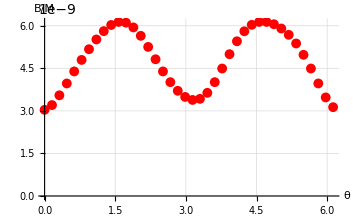
1/-Graphics-

```mathematica
1/Out[42]
```

```mathematica
Tan[0.5]
```

0.546302

```mathematica
BYZplane[0,14.34*10^-2]
```

1.38345×10^-10

```mathematica
BYZplane[0.3,14.34*10^-2]
```

1.5758×10^-10

```mathematica
B5p0=Table[{(π*x)/20,BYZplane[(π*x)/20,5.0*10^-2]},{x,0,39}]
```

NIntegrate::ilim: Invalid integration variable or limit(s) in {0,y,z}∈Ellipsoid[{0,0,0},{0.021,0.0069,0.0069}].

General::stop: Further output of NIntegrate::ilim will be suppressed during this calculation.

{{0,3.03726×10^-9},{π/20,3.20503×10^-9},{π/10,3.54882×10^-9},{(3 π)/20,3.9659×10^-9},{π/5,4.39068×10^-9},{π/4,4.79574×10^-9},{(3 π)/10,5.17342×10^-9},{(7 π)/20,5.51732×10^-9},{(2 π)/5,5.81117×10^-9},{(9 π)/20,6.02763×10^-9},{π/2,6.13534×10^-9},{(11 π)/20,6.10955×10^-9},{(3 π)/5,5.94176×10^-9},{(13 π)/20,5.64518×10^-9},{(7 π)/10,5.25436×10^-9},{(3 π)/4,4.81868×10^-9},{(4 π)/5,4.39053×10^-9},{(17 π)/20,4.01193×10^-9},{(9 π)/10,3.70762×10^-9},{(19 π)/20,3.49188×10^-9},{π,3.38562×10^-9},{(21 π)/20,3.42409×10^-9},{(11 π)/10,3.6365×10^-9},{(23 π)/20,4.01225×10^-9},{(6 π)/5,4.4933×10^-9},{(5 π)/4,4.99872×10^-9},{(13 π)/10,5.4535×10^-9},{(27 π)/20,5.80562×10^-9},{(7 π)/5,6.03195×10^-9},{(29 π)/20,6.13541×10^-9},{(3 π)/2,6.13534×10^-9},{(31 π)/20,6.05385×10^-9},{(8 π)/5,5.90335×10^-9},{(33 π)/20,5.68137×10^-9},{(17 π)/10,5.37556×10^-9},{(7 π)/4,4.97661×10^-9},{(9 π)/5,4.49345×10^-9},{(37 π)/20,3.96622×10^-9},{(19 π)/10,3.47445×10^-9},{(39 π)/20,3.13104×10^-9}}

```mathematica
B9p5=Table[{(π*x)/20,BYZplane[(π*x)/20,9.5*10^-2]},{x,0,39}]
```

NIntegrate::ilim: Invalid integration variable or limit(s) in {0,y,z}∈Ellipsoid[{0,0,0},{0.021,0.0069,0.0069}].

General::stop: Further output of NIntegrate::ilim will be suppressed during this calculation.

{{0,4.67775×10^-10},{π/20,4.90022×10^-10},{π/10,5.41226×10^-10},{(3 π)/20,6.07424×10^-10},{π/5,6.77903×10^-10},{π/4,7.4642×10^-10},{(3 π)/10,8.09502×10^-10},{(7 π)/20,8.64573×10^-10},{(2 π)/5,9.0884×10^-10},{(9 π)/20,9.39068×10^-10},{π/2,9.52094×10^-10},{(11 π)/20,9.45684×10^-10},{(3 π)/5,9.19352×10^-10},{(13 π)/20,8.74809×10^-10},{(7 π)/10,8.1592×10^-10},{(3 π)/4,7.4817×10^-10},{(4 π)/5,6.77844×10^-10},{(17 π)/20,6.11283×10^-10},{(9 π)/10,5.54669×10^-10},{(19 π)/20,5.14423×10^-10},{π,4.97345×10^-10},{(21 π)/20,5.08748×10^-10},{(11 π)/10,5.48893×10^-10},{(23 π)/20,6.11561×10^-10},{(6 π)/5,6.86545×10^-10},{(5 π)/4,7.63157×10^-10},{(13 π)/10,8.32417×10^-10},{(27 π)/20,8.88065×10^-10},{(7 π)/5,9.26782×10^-10},{(29 π)/20,9.47807×10^-10},{(3 π)/2,9.52094×10^-10},{(31 π)/20,9.41206×10^-10},{(8 π)/5,9.16356×10^-10},{(33 π)/20,8.77984×10^-10},{(17 π)/10,8.26126×10^-10},{(7 π)/4,7.61441×10^-10},{(9 π)/5,6.86604×10^-10},{(37 π)/20,6.07704×10^-10},{(19 π)/10,5.35305×10^-10},{(39 π)/20,4.84061×10^-10}}

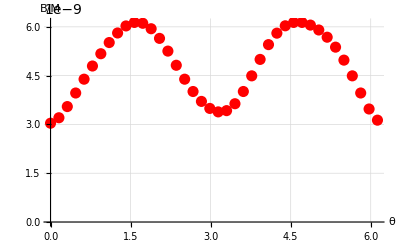

```mathematica
ListPlot[B5p0,PlotStyle->{Red,PointSize[0.02]},AxesLabel->{"θ","B/M"},PlotRange->All,GridLines->Automatic]
```

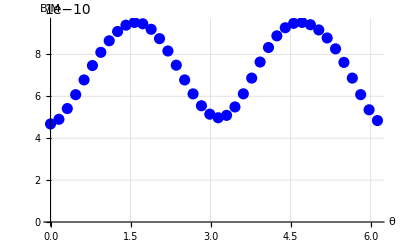

```mathematica
ListPlot[B9p5,PlotStyle->{Blue,PointSize[0.02]},AxesLabel->{"θ","B/M"},PlotRange->All,GridLines->Automatic]
```

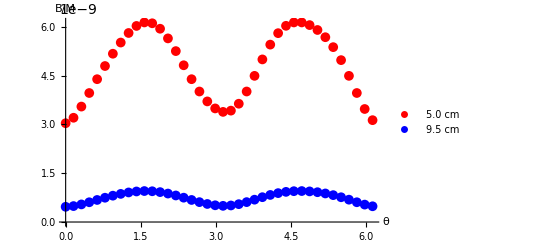

```mathematica
ListPlot[{B5p0,B9p5},PlotStyle->{Red,Blue},PlotMarkers->{"●",10},AxesLabel->{"θ","B/M"},PlotLegends->{"5.0 cm","9.5 cm"}]
```

```mathematica
BRto=Table[{x,Total[Select[B5p0,#[[1]]==x&][[All,2]]]/Total[Select[B9p5,#[[1]]==x&][[All,2]]]},{x,Union[B5p0[[All,1]]]}]
```

{{0,6.49299},{π/20,6.54059},{π/10,6.55701},{(3 π)/20,6.52905},{π/5,6.47685},{π/4,6.425},{(3 π)/10,6.39087},{(7 π)/20,6.38155},{(2 π)/5,6.39405},{(9 π)/20,6.41874},{π/2,6.44405},{(11 π)/20,6.46045},{(3 π)/5,6.46299},{(13 π)/20,6.45304},{(7 π)/10,6.43979},{(3 π)/4,6.44063},{(4 π)/5,6.47719},{(17 π)/20,6.56314},{(9 π)/10,6.68439},{(19 π)/20,6.78795},{π,6.8074},{(21 π)/20,6.73042},{(11 π)/10,6.62516},{(23 π)/20,6.56066},{(6 π)/5,6.5448},{(5 π)/4,6.55006},{(13 π)/10,6.5514},{(27 π)/20,6.53738},{(7 π)/5,6.50849},{(29 π)/20,6.47327},{(3 π)/2,6.44405},{(31 π)/20,6.43201},{(8 π)/5,6.44221},{(33 π)/20,6.47093},{(17 π)/10,6.50695},{(7 π)/4,6.53578},{(9 π)/5,6.54445},{(37 π)/20,6.52656},{(19 π)/10,6.49061},{(39 π)/20,6.46828}}

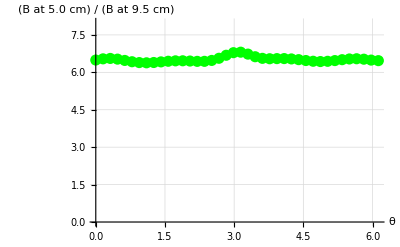

```mathematica
ListPlot[BRto,PlotStyle->{Green,PointSize[0.02]},AxesLabel->{"θ","(B at 5.0 cm) / (B at 9.5 cm)"},PlotRange->{Automatic,{0,8}},GridLines->Automatic]
```

```mathematica
Mean[BRto].{0,1}
```

6.51428

It is important to say this here:

The datasets B5p0 and B9p5 are the theoretical values of the B-fields, taken to be measured at 5.0 cm and 9.5 cm respectively from the CM of the magnet (same setup as experimental).
Note in particular that B5p0 and B9p5 are NEVER equal to zero for all values of theta -- THIS IS TO BE EXPECTED! However, we normalized the B-fields experimentally to get rid of the background
fields, thus we must normalize the fields here as well. Thus the datasets B5p0nm and B9p5nm are the normalized B-fields -- we make the average of the points zero -- i.e. move all the data points
down by some fixed amount.

So how to calculate M? Recall that these values all assume that M = 1 -- well, we simply take ratios: [experimental amplitude] / [theoretical amplitude when M = 1] on the normalized data sets, which is fine
because normalization = shifting things down, the amplitude value is not changed at all. Also note that using either the 5.0 cm dataset or the 9.5 cm data set should give a similar value of M --
the ratio B5p0 / B9p5 is roughly constant and equal to 6.6 and this matches experimental ratio of these values still.

ALSO a very important thing: average value of the ratio B5p0 / B9p5 is about 6.51, but the mean of the ratio B5p0nm / B9p5nm drops to 6.23. The experimental mean of the same value is about 6.8.
The 6.51 value is CLOSER to the true average value. This is because there is less noise due to the sinusoidal wave -- especially because we are taking discrete measurements which would be a major source
of outliers the values are close to zero. In fact, this is exactly the reason why in the experimental data we threw out six outliers since they were TOO CLOSE to zero (ok think about it like this --
if x changes from 4 to 3.9 then 1/x doesn’t change much, but when x changes from 1 to 0.9 then 1/x changes much more even though x changes by same amount. so the experimental error would be
magnified by a huge amount which is bad). --> to get 6.8 avg.

```mathematica
B5p0nm=(-{0,Mean[B5p0].{0,1}}+B5p0ᵀ)ᵀ
```

{{0,-1.75144×10^-9},{π/20,-1.58367×10^-9},{π/10,-1.23988×10^-9},{(3 π)/20,-8.228×10^-10},{π/5,-3.98025×10^-10},{π/4,7.04236×10^-12},{(3 π)/10,3.84724×10^-10},{(7 π)/20,7.28621×10^-10},{(2 π)/5,1.02247×10^-9},{(9 π)/20,1.23893×10^-9},{π/2,1.34664×10^-9},{(11 π)/20,1.32085×10^-9},{(3 π)/5,1.15306×10^-9},{(13 π)/20,8.56481×10^-10},{(7 π)/10,4.65659×10^-10},{(3 π)/4,2.99833×10^-11},{(4 π)/5,-3.98172×10^-10},{(17 π)/20,-7.76766×10^-10},{(9 π)/10,-1.08108×10^-9},{(19 π)/20,-1.29682×10^-9},{π,-1.40308×10^-9},{(21 π)/20,-1.36461×10^-9},{(11 π)/10,-1.1522×10^-9},{(23 π)/20,-7.76452×10^-10},{(6 π)/5,-2.95398×10^-10},{(5 π)/4,2.10023×10^-10},{(13 π)/10,6.64795×10^-10},{(27 π)/20,1.01692×10^-9},{(7 π)/5,1.24325×10^-9},{(29 π)/20,1.34671×10^-9},{(3 π)/2,1.34664×10^-9},{(31 π)/20,1.26515×10^-9},{(8 π)/5,1.11465×10^-9},{(33 π)/20,8.9267×10^-10},{(17 π)/10,5.86858×10^-10},{(7 π)/4,1.87912×10^-10},{(9 π)/5,-2.95255×10^-10},{(37 π)/20,-8.22483×10^-10},{(19 π)/10,-1.31425×10^-9},{(39 π)/20,-1.65766×10^-9}}

```mathematica
B9p5nm=(-{0,Mean[B9p5].{0,1}}+B9p5ᵀ)ᵀ
```

{{0,-2.68905×10^-10},{π/20,-2.46658×10^-10},{π/10,-1.95454×10^-10},{(3 π)/20,-1.29256×10^-10},{π/5,-5.87767×10^-11},{π/4,9.73953×10^-12},{(3 π)/10,7.28219×10^-11},{(7 π)/20,1.27893×10^-10},{(2 π)/5,1.7216×10^-10},{(9 π)/20,2.02388×10^-10},{π/2,2.15414×10^-10},{(11 π)/20,2.09004×10^-10},{(3 π)/5,1.82672×10^-10},{(13 π)/20,1.38129×10^-10},{(7 π)/10,7.92403×10^-11},{(3 π)/4,1.149×10^-11},{(4 π)/5,-5.88357×10^-11},{(17 π)/20,-1.25397×10^-10},{(9 π)/10,-1.82011×10^-10},{(19 π)/20,-2.22257×10^-10},{π,-2.39335×10^-10},{(21 π)/20,-2.27932×10^-10},{(11 π)/10,-1.87788×10^-10},{(23 π)/20,-1.25119×10^-10},{(6 π)/5,-5.01346×10^-11},{(5 π)/4,2.64767×10^-11},{(13 π)/10,9.57364×10^-11},{(27 π)/20,1.51385×10^-10},{(7 π)/5,1.90102×10^-10},{(29 π)/20,2.11127×10^-10},{(3 π)/2,2.15414×10^-10},{(31 π)/20,2.04526×10^-10},{(8 π)/5,1.79676×10^-10},{(33 π)/20,1.41304×10^-10},{(17 π)/10,8.94461×10^-11},{(7 π)/4,2.47607×10^-11},{(9 π)/5,-5.00764×10^-11},{(37 π)/20,-1.28976×10^-10},{(19 π)/10,-2.01375×10^-10},{(39 π)/20,-2.52619×10^-10}}

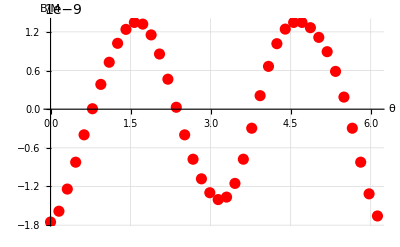

```mathematica
ListPlot[B5p0nm,PlotStyle->{Red,PointSize[0.02]},AxesLabel->{"θ","B/M"},PlotRange->All,GridLines->Automatic]
```

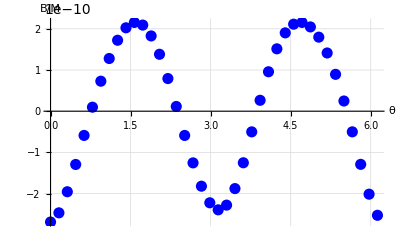

```mathematica
ListPlot[B9p5nm,PlotStyle->{Blue,PointSize[0.02]},AxesLabel->{"θ","B/M"},PlotRange->All,GridLines->Automatic]
```

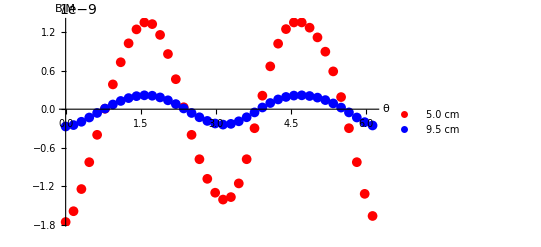

```mathematica
ListPlot[{B5p0nm,B9p5nm},PlotStyle->{Red,Blue},PlotMarkers->{"●",10},AxesLabel->{"θ","B/M"},PlotLegends->{"5.0 cm","9.5 cm"}]
```

```mathematica
MAGNETIZATION=Min[(0.89264*10^-3)/Max[B5p0nm.{0,1}],(0.13604*10^-3)/Max[B9p5nm.{0,1}]] (* the numerators are the magnetic field obtained experimentally (by Govind & Michael), these are in mT
hence the 10^-3 factor. the denominators are the maxima of the B5p0nm and B9p5nm datasets which determine the amplitude -- this is THE only use of the
B5p0nm and B9p5nm datasets *)
```

631528.

## §3. Period of Out-of-Plane Oscillations